# Covs

```mathematica
utIdxs=Flatten[Table[5*(j-1)+i,{j,5},{i,j,5}]]
```

{1,2,3,4,5,7,8,9,10,13,14,15,19,20,25}

```mathematica
SetDirectory[NotebookDirectory[]];
covData=Import["data/cov_mat.txt","Table"];
opts=covData[[;;,1]];

covs={};
Do[
i=k+1;
covVec=covData[[;;,i]];
AppendTo[covs,Transpose[{opts,covVec}]];
,{k,utIdxs}];
```

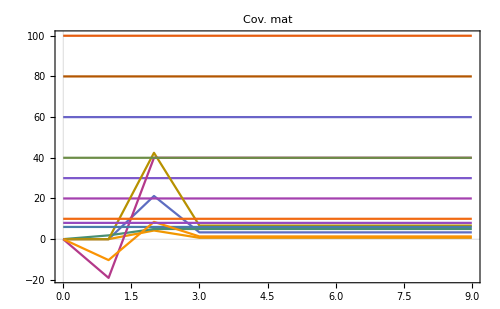

```mathematica
pCov=Show[
ListLinePlot[covs],
ImageSize->500,
PlotLabel->"Cov. mat",
FrameLabel->{"Optimization step"}
]
```

```mathematica
CreateDirectory["figures"];
Export["figures/cov.png",pCov,ImageResolution->200]
```

CreateDirectory::filex: /Users/oernst/software_private/ggm_inversion/test/output/root_find_newton_5d/figures already exists.

figures/cov.png

# Prec mat

```mathematica
SetDirectory[NotebookDirectory[]];
precData=Import["data/prec_mat.txt","Table"];
opts=precData[[;;,1]];

precs={};
Do[
i=k+1;
precVec=precData[[;;,i]];
AppendTo[precs,Transpose[{opts,precVec}]];
,{k,utIdxs}];
```

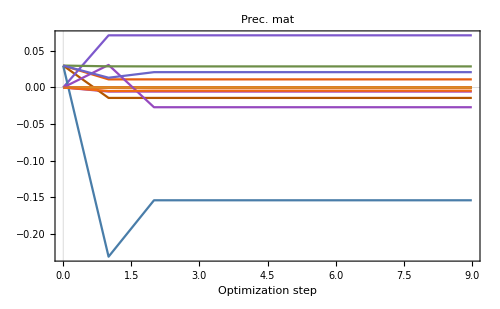

```mathematica
pPrec=ListLinePlot[precs,PlotRange->All,PlotLabel->"Prec. mat",FrameLabel->{"Optimization step"},ImageSize->500]
```

```mathematica
CreateDirectory["figures"];
Export["figures/prec.png",pPrec,ImageResolution->200]
```

CreateDirectory::filex: /Users/oernst/software_private/ggm_inversion/test/output/root_find_newton_5d/figures already exists.

figures/prec.png

# Invert prec mat

```mathematica
SetDirectory[NotebookDirectory[]];
precData=Import["data/prec_mat.txt","Table"];
opts=precData[[;;,1]];

covsPrec0={};
Do[
precVec=precData[[optPt,2;;]];
precMat=ArrayReshape[precVec,{5,5}];
covMat=Inverse[precMat];
covVec=Flatten[covMat];
cov=covVec[[utIdxs]];

AppendTo[covsPrec0,cov];
,{optPt,Length[precData]}];

covsPrec={};
Do[
cp=covsPrec0[[;;,i]];
AppendTo[covsPrec,Transpose[{opts,cp}]];
,{i,Length[cov]}];
```

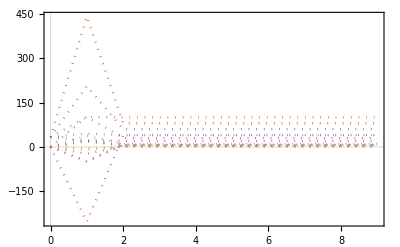

```mathematica
pInv=ListLinePlot[covsPrec,PlotRange->All,PlotStyle->Dotted]
```

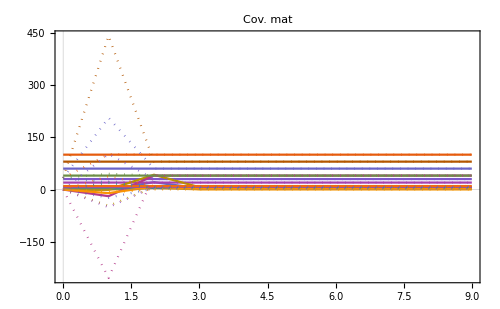

```mathematica
pCovTog=Show[pCov,pInv,PlotRange->All]
```

```mathematica
CreateDirectory["figures"];
Export["figures/cov_tog.png",pCovTog,ImageResolution->200]
```

CreateDirectory::filex: /Users/oernst/software_private/ggm_inversion/test/output/root_find_newton_5d/figures already exists.

figures/cov_tog.png

# Residuals

```mathematica
precData=Import["data/prec_mat.txt","Table"];
covData=Import["data/cov_mat.txt","Table"];

residuals={};
Do[
precMat=ArrayReshape[precData[[optStep,2;;]],{5,5}];
covMat=ArrayReshape[covData[[optStep,2;;]],{5,5}];

residuals0=Flatten[precMat.covMat-IdentityMatrix[5]];
residuals0=residuals0[[utIdxs]];
AppendTo[residuals,residuals0];
,{optStep,Length[precData]}];
```

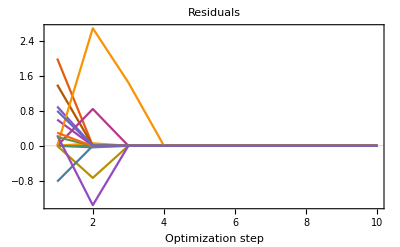

```mathematica
pRes=ListLinePlot[Transpose[residuals],PlotRange->All,PlotLabel->"Residuals",FrameLabel->{"Optimization step"}]
```

```mathematica
CreateDirectory["figures"];
Export["figures/residuals.png",pRes,ImageResolution->200]
```

CreateDirectory::filex: /Users/oernst/software_private/ggm_inversion/test/output/root_find_newton_5d/figures already exists.

figures/residuals.png